# Developing Device Drivers

Overviewpaclet:tutorial/DevelopingDeviceDrivers#939564002 | Inheritancepaclet:tutorial/DevelopingDeviceDrivers#699998962
Device Driver Optionspaclet:tutorial/DevelopingDeviceDrivers#602846093 | Miscellaneous Notespaclet:tutorial/DevelopingDeviceDrivers#1166042701
Device Framework Functionspaclet:tutorial/DevelopingDeviceDrivers#617176298 | Developing Device Driver Pacletspaclet:tutorial/DevelopingDeviceDrivers#1883152198
Device Propertiespaclet:tutorial/DevelopingDeviceDrivers#720023240 | Examplespaclet:tutorial/DevelopingDeviceDrivers#647897357
Device Discoverypaclet:tutorial/DevelopingDeviceDrivers#2076911133 | Further Infopaclet:tutorial/DevelopingDeviceDrivers#1293143377

The Wolfram Device Framework, built into the Wolfram Language, creates symbolic objects that represent external devices, streamlines interaction with devices, and facilitates the authoring of device drivers. This tutorial explains the internals of the Device Framework for advanced users and developers of device drivers. For details of the interaction with devices at the user level, see "Using Connected Devices".

For most devices, the functions that comprise the Device Framework are not directly concerned with actual device programming or low-level hardware communication software. Such implementation would vary on a case-by-case basis depending on the hardware device in question. For instance, one implementation might involve writing (or being supplied with by a third party) low-level device programs in C, and then using WSTP to expose the interfaces of these programs to package-level Wolfram Language functions. These functions would then be strung together in an appropriate fashion by the Device Framework, creating a Wolfram Language device driver. In another implementation, one might avoid low-level C programming altogether and use the Wolfram Language .NET/Link functionality to interact with a device from within driver-level Wolfram Language functions. The responsibility of the Device Framework would again be to integrate these functions, providing a unified way of interfacing with devices through a set of user-level functions.

## Overview

```mathematica
$Line=0;Clear["DevelopingDeviceDrivers`*"];DeviceFramework`DeviceDeregister[Devices[]];
```

Developer-level functions for creating device drivers and encapsulating lower-level interactions with devices are collected in the DeviceFramework` context, see "Device Framework Functions". At the heart of a device driver is the function DeviceClassRegister.

DeviceFramework`DeviceClassRegister["class",opts] | 
 | register a device driver for the specified class whose operation is defined by the options opts 
DeviceFramework`DeviceClassRegister["class","parent",opts] | 
 | register a class identical to parent, except for operations defined by the options opts

Options of DeviceClassRegister determine various device and driver properties and define functions that the framework will call to discover devices of the class and execute operations that a generic device is expected to perform, such as opening a connection to a device, configuring it, reading from and writing to a device, executing a command, and closing the connection to a device and releasing external resources.

option | default value | 
"FindFunction" | {}& | how to discover devices
"OpenFunction" | None | the function to execute when opening a device
"ConfigureFunction" | None | how to configure a device
"ReadFunction" | None | how to read from a device
"ReadBufferFunction" | None | how to read from a device buffer
"WriteFunction" | None | how to write to a device
"WriteBufferFunction" | None | how to write to a device buffer
"ExecuteFunction" | None | how to execute a command on a device
"ExecuteAsynchronousFunction" | None | how to execute a command asyncronously
"CloseFunction" | None | the function to execute when closing a device
"Properties" | {} | standardized properties
"DeviceIconFunction" | None | how to create an icon for the device object
"DriverVersion" | Missing["NotAvailable"] | the version number of the driver

Important device driver options.

A more general workflow could involve creating a device manager (an initialization object and its handle) before opening a device and preconfiguring device properties before exposing a new device object to the user. The initialization object would then be disposed of at the release stage after the device is closed.

It is also possible to define handlers for setting and getting standardized device properties, exposing native device properties and methods, and giving the user access to input and output streams associated with a device. Finally, a driver can define a policy for creating multiple devices of the class as well as specify other custom handlers.

option | default value | 
"OpenManagerFunction" | None | the function to execute to open a device manager
"MakeManagerHandleFunction" | Identity | how to create a handle to the device manager
"PreconfigureFunction" | {}& | how to preconfigure a new device
"ReleaseFunction" | Null& | how to dispose of the device manager object
"ReadTimeSeriesFunction" | Automatic | the handler for DeviceReadTimeSeriespaclet:ref/DeviceReadTimeSeries
"StatusLabelFunction" | Automatic | how to create the status label for the device object
"NativeProperties" | {} | native properties
"NativeMethods" | {} | native methods
"GetPropertyFunction" | DeviceFramework`DeviceGetProperty | how to get standardized properties
"SetPropertyFunction" | DeviceFramework`DeviceSetProperty | how to set standardized properties
"GetNativePropertyFunction" | Automatic | how to get native properties
"SetNativePropertyFunction" | Automatic | how to set native properties
"NativeIDFunction" | None | how to get the native ID of a device
"OpenReadFunction" | None | how to open input streams assoociated with the device
"OpenWriteFunction" | None | how to open output streams assoociated with the device
"DeregisterOnClose" | False | whether to deregister a device after it is closed
"Singleton" | Automatic | creation policy for multiiple devices

Advanced device driver options.

A detailed look at the DeviceClassRegister options follows in the next section. Note that none of the options are mandatory and many of them would typically be omitted in a particular driver implementation.

As an example, here is a driver for a simple device that can perform the device read operation:

BeginPackage["MyDevice`"]

Begin["`Private`"]

read[__] := XXXXX

DeviceFramework`DeviceClassRegister["MyDevice", "ReadFunction" → read]

End[]

EndPackage[]

A basic driver file MyDevice.m.

To be automatically discoverable by the framework, a DeviceClassRegister["class",…] statement for class must reside in a Wolfram Language package class.m. Note the naming convention; the first string argument of DeviceClassRegister matches the driver file name. Further, the driver must be placed at one of the following locations:

in the current evaluation notebook directory (NotebookDirectorypaclet:ref/NotebookDirectory)

in a special directory ToFileNamepaclet:ref/ToFileName[{$InstallationDirectorypaclet:ref/$InstallationDirectory,"SystemFiles","Devices","DeviceDrivers"}] on your computer system

anywhere on $Pathpaclet:ref/$Path

on a paclet server or in a driver paclet directory (see "Developing Device Driver Paclets")

A driver can be used even if it does not follow these conventions, but then it must be explicitly loaded in your Wolfram Language session, for instance, with Getpaclet:ref/Get.

To make a driver available on a specific platform, you can wrap a DeviceClassRegister[] statement in an Ifpaclet:ref/If.

This driver will only be available on Mac OS X.

```mathematica
If[$OperatingSystem==="MacOSX",DeviceFramework`DeviceClassRegister["mac"];]
```

## Device Driver Options

The options of DeviceClassRegister, also called device driver options, allow you to create a driver suitable for your device. Driver options whose names include the word "Function" (driver functions) roughly correspond to user-level functions. For instance, "ConfigureFunction" is called during the execution of DeviceConfigurepaclet:ref/DeviceConfigure, "FindFunction" is called in FindDevicespaclet:ref/FindDevices, and so on. However, there are also user-level functions that span more than one driver function, as indicated below. One example is the device opening sequence, executed during DeviceOpenpaclet:ref/DeviceOpen, that includes "OpenManagerFunction", "MakeManagerHandleFunction", "OpenFunction", and "PreconfigureFunction". If a driver function fails, it is expected to return $Failedpaclet:ref/$Failed.

The first argument supplied to many driver functions is a list in the form {ihandle, dhandle}, where ihandle is the handle to the initialization object (or manager handle; see "MakeManagerHandleFunction") and dhandle is the device handle (see "OpenFunction"). This convention, employed in "ConfigureFunction", "ReadFunction", and other driver functions, lets you use whatever handle is necessary and skip the other one. For instance, if you only need ihandle, your driver function could be implemented as f[{ih_, _}, args___]:=(* use ih *); to use only dhandle, you provide a rule for f[{_, dh_}, args___]:=…; to skip both handles, use f[_, args___]:=…; and so on. You will find many examples of such usage below.

The remaining arguments supplied to a driver function are typically passed from the parent top-level function, possibly stripped of a list wrapper. For instance, for both DeviceReadpaclet:ref/DeviceRead[dev,param] and DeviceReadpaclet:ref/DeviceRead[dev,{param}], your implementation of "ReadFunction"→f will receive a call as f[handles,param]; for DeviceReadpaclet:ref/DeviceRead[dev,{param_1,param_2,…}], the function will be called as f[handles,param_1,param_2,…]; for DeviceReadpaclet:ref/DeviceRead[dev], the call will be in the form f[handles], and so on. You should anticipate all possible combinations of arguments that are documented for the parent function and issue appropriate error messages if some combinations do not make sense in your case.

When reporting errors, it is customary to associate messages with your own user-visible symbols if your driver exports such symbols. Otherwise, you can assign messages for your class to a special symbol DeviceFramework`Devices`class. Some examples of this convention are given in this tutorial. To learn more, see "Messages".

Of course, if your driver does not implement some driver functions, you need not bother about error messages for those functions either. Such messages are issued by the framework.

This dummy driver does not implement any driver functions.

```mathematica
DeviceFramework`DeviceClassRegister["dummy"]
```

dummy

You can open a dummy device, but attempting to execute any specific operation on it will result in error.

```mathematica
dev=DeviceOpen["dummy"]
```

DeviceObject[…]

```mathematica
DeviceConfigure[dev,a->x]
```

DeviceConfigure::noop: DeviceConfigure not supported for "dummy".

$Failed

In reading through this tutorial, you will have noticed that most examples employ only top-level Wolfram Language commands. This is done on purpose so that you could reevaluate examples and learn to use the device framework without any specific device. Real-life drivers will, of course, also call external programs. See "Calling External Programs" for an overview and the "Examples" section below for a typical implementation.

Besides examples in this tutorial, you might also want to look over the implementation of demo drivers referenced in the Wolfram Language documentation. For instance, to see how you could implement "ExecuteAsynchronousFunction", look at the demo driver for DeviceExecuteAsynchronouspaclet:ref/DeviceExecuteAsynchronous.

Execute the following command to examine a demo implementation of "ExecuteAsynchronousFunction".

```mathematica
DeviceFramework`DeviceDriverLoad["AsynchronousDemo"]//SystemOpen
```

### "FindFunction"

In order for your device to be discoverable, your driver must implement the "FindFunction" option. "FindFunction"→f specifies that f[] should be called by FindDevicespaclet:ref/FindDevices[class] to find devices of the given class. The function f receives no arguments and should return an output in the form {{arg_11,arg_12,…},{arg_21,arg_22,…},…}, where {arg_i1,arg_i2,…} is a list of arguments that could be supplied to DeviceOpenpaclet:ref/DeviceOpen[class,{arg_i1,arg_i2,…}] to open the device number i.

Typical arguments returned by the function f would be a port name, a GPIB address, or a camera name. If a device can be opened without arguments, f can return {{}}&.

If your driver implements "FindFunction", the user will also be able to use devices of your class without explicitly opening them first.

Devices without a proper "FindFunction" are not automatically discoverable.

```mathematica
DeviceFramework`DeviceClassRegister["read","ReadFunction"->(Random[]&)]
```

read

```mathematica
FindDevices["read"]
```

{}

You must open a device of such class before it can be used.

```mathematica
DeviceRead["read"]
```

DeviceRead::ncdevx: Unable to automatically open a device in the "read" class to perform this operation. Try opening a device first.

$Failed

```mathematica
DeviceOpen["read"]
```

DeviceObject[…]

```mathematica
DeviceRead["read"]
```

0.156006

This driver extends the previous one by supplying the "FindFunction" option.

```mathematica
DeviceFramework`DeviceClassRegister["read2","read","FindFunction"->({{}}&)]
```

read2

Devices of this class can be opened automatically by the framework.

```mathematica
DeviceRead["read2"]
```

0.537186

Devices remain open after performing the required operation until they are explicitly closed.

```mathematica
Devices["read2"]
```

{DeviceObject[…]}

```mathematica
DeviceClose[%]
```

{Null}

### "OpenManagerFunction"

"OpenManagerFunction"→f specifies that f[args…] should be called at the outset of the device opening sequence to create an initialization object, also called the "device manager". args are the same as the user supplies to DeviceOpenpaclet:ref/DeviceOpen["class",{args…}]. The return value will be passed to "ReleaseFunction" in the deinitialization stage at the end of the device life cycle. Use DeviceFramework`DeviceInitObject to retrieve the initialization object at any other time before the device is closed.

You may wish to specify "OpenManagerFunction", for instance, to open a WSTP connection to an external program. In that case, the function would return a LinkObjectpaclet:ref/LinkObject, which you can close with LinkClosepaclet:ref/LinkClose in your "ReleaseFunction".

This driver keeps a count of open devices in the class.

```mathematica
DeviceFramework`DeviceClassRegister["count","OpenManagerFunction"->(($counter++)&),"ReleaseFunction"->(($counter--)&)];
```

The counter is incremented (decremented) when a device is opened (closed).

```mathematica
$counter = 0;
```

```mathematica
dev=DeviceOpen["count"]
```

DeviceObject[…]

```mathematica
$counter
```

1

```mathematica
DeviceClose[dev];$counter
```

0

### "MakeManagerHandleFunction"

You can create a separate handle to the initialization object (a manager handle) by specifying "MakeManagerHandleFunction"→f. The function f[obj] will be called after "OpenManagerFunction" and supplied the initialization object obj created by "OpenManagerFunction". The return value is assumed to be the manager handle. In the absence of "MakeManagerHandleFunction", the manager handle will be the initialization object itself.

The manager handle is given to many driver functions as a part of the first argument. At other times, you can retrieve the handle with DeviceFramework`DeviceManagerHandle.

An example of a manager handle would be a socket handle or a .NET object.

### "OpenFunction"

The function specified with "OpenFunction"→f is the main function called by the framework in response to a user call to DeviceOpenpaclet:ref/DeviceOpen.  f[ihandle,args…] receives the manager handle ihandle created by "MakeManagerHandleFunction" and the arguments args the user supplies to DeviceOpenpaclet:ref/DeviceOpen["class",{args…}]. The return value is called the "device handle". That handle will be given to many driver functions along with the manager handle (see below). Otherwise, you can retrieve it with DeviceFramework`DeviceHandle.

The framework attempts to maintain a one-to-one correspondence between the device handle returned by "OpenFunction" and the top-level DeviceObjectpaclet:ref/DeviceObject returned by DeviceOpenpaclet:ref/DeviceOpen. It is therefore strongly recommended that your device handles be unique or at least unlikely to coincide with handles created by other drivers. One easy way to achieve that is to generate your handle using CreateUUIDpaclet:ref/CreateUUID. Alternatively, you can return a handle in the form "com.company.class"[… ] or use similar means.

Devices of this class print open arguments. The ihandle parameter is not used.

```mathematica
open[_,args___] := (Print[{args}];CreateUUID[])
```

```mathematica
DeviceFramework`DeviceClassRegister["print","OpenFunction"->open];
```

```mathematica
dev=DeviceOpen["print",1]
```

{1}

DeviceObject[…]

Retrieve the device handle and use it to get back the device object.

```mathematica
DeviceFramework`DeviceHandle[dev]
```

08b1a825-408b-46fc-95b7-14afedcf8a92

```mathematica
DeviceFramework`DeviceObjectFromHandle[%]
```

DeviceObject[…]

If "OpenFunction" is omitted, the framework assigns a random device handle to any new device in the class.

This driver does not implement "OpenFunction".

```mathematica
DeviceFramework`DeviceClassRegister["nopen"];
```

```mathematica
dev=DeviceOpen["nopen"]
```

DeviceObject[…]

You can still use the default device handle provided by the framework.

```mathematica
DeviceFramework`DeviceHandle[dev]//DeviceFramework`DeviceObjectFromHandle
```

DeviceObject[…]

### "PreconfigureFunction"

The function specified in "PreconfigureFunction"→f concludes the device opening sequence. For the device object dev that is about to be returned to the user, f[dev] is guaranteed to be called at the end of a successful call to DeviceOpenpaclet:ref/DeviceOpen, but before the initial configuration that re-applies top-level device properties of the device (if they have been set on the device previously) or sets class properties (if they are defined by the driver). "PreconfigureFunction" must return a list of properties that has been configured by the driver, by "PreconfigureFunction" itself, "OpenFunction", or any other function in the device opening sequence. These properties will not be changed further by the framework until DeviceOpenpaclet:ref/DeviceOpen finishes. Allpaclet:ref/All or Nonepaclet:ref/None can also be returned.

This driver sets a device property "parity" based on the device ID.

```mathematica
DeviceFramework`DeviceClassRegister["p","Properties"->{"parity"->Null},"PreconfigureFunction"->((#["parity"]=If[EvenQ[DeviceFramework`DeviceID[#]],"even","odd"];All)&)];
```

```mathematica
dev=DeviceOpen["p"]
```

DeviceObject[…]

```mathematica
dev["parity"]
```

odd

"PreconfigureFunction" is also a convenient place to set status labels for the open and closed device states.

This driver automatically closes an open device after 20 seconds and displays a running indicator of time until close.

```mathematica
DeviceFramework`DeviceClassRegister["timeout","PreconfigureFunction"->With[{max=20},($timeout=0;DeviceFramework`DeviceStatusLabels[#]={ProgressIndicator[Dynamic[$timeout],{0,max},ImageSize->{20,3}],"Closed"};RunScheduledTask[If[++$timeout≥max,DeviceClose[#]],{0.1,max},"AutoRemove"->True];None)&]];
```

```mathematica
dev=DeviceOpen["timeout"]
```

DeviceObject[…]

### "ConfigureFunction"

"ConfigureFunction"→f specifies that f[{ihandle,dhandle},args…] should be called in response to the top-level command DeviceConfigurepaclet:ref/DeviceConfigure[dev,{args…}] to configure a device. The first argument {ihandle,dhandle}, where ihandle is the manager handle and dhandle is the device handle, is common to many driver functions. The return value of this function is not used, unless it is $Failedpaclet:ref/$Failed.

"ConfigureFunction" in this driver sets a top-level property.

```mathematica
config[{_,h_},assoc_]:=With[{dev=DeviceFramework`DeviceObjectFromHandle[h]},dev["p"]=Lookup[assoc,"p"]]
```

```mathematica
DeviceFramework`DeviceClassRegister["c","Properties"->{"p"->1},"ConfigureFunction"->config];
```

Open a device and configure it by calling DeviceConfigurepaclet:ref/DeviceConfigure.

```mathematica
dev=DeviceOpen["c"]
```

DeviceObject[…]

```mathematica
DeviceConfigure[dev,"p"->"new"]
```

p→new

This is the new value of the property.

```mathematica
dev["p"]
```

new

### "ReadFunction"

"ReadFunction"→f specifies that f[{ihandle,dhandle},args…] should be called in response to the top-level command DeviceReadpaclet:ref/DeviceRead[dev,{args…}] to read data from a device. The first argument {ihandle,dhandle}, where ihandle is the manager handle and dhandle is the device handle, is common to many driver functions. The return value of this function will be passed on to the user as an output of the DeviceReadpaclet:ref/DeviceRead[] command.

Devices of this class read consecutive characters from a string. The current string position for each device is stored in an association, with device handles as keys. Keys are added to the association in "OpenFunction" and removed in "CloseFunction".

```mathematica
$string="abcde";
```

```mathematica
$positions=<||>;
```

```mathematica
read[{_,h_}]:=StringTake[$string,{++$positions[h]}]/;$positions[h]<5
```

```mathematica
read[___]:=$Failed
```

```mathematica
open[___]:=Module[{h=CreateUUID[]},$positions[h]=0;h]
```

```mathematica
close[{_,h_},___]:=$positions[h]=.
```

```mathematica
DeviceFramework`DeviceClassRegister["r","ReadFunction"->read,"OpenFunction"->open,"CloseFunction"->close];
```

Open a device and read a character from it.

```mathematica
dev1=DeviceOpen["r",1]
```

DeviceObject[…]

```mathematica
DeviceRead[dev1]
```

a

Open another device and read several characters.

```mathematica
dev2=DeviceOpen["r",2]
```

DeviceObject[…]

```mathematica
DeviceReadList[dev2,3]
```

{a,b,c}

The current read counters are remembered for each open device.

```mathematica
$positions
```

<|0bc917c3-22a5-44be-8e0b-dea2cd2f7985→1,36c8bd52-9e61-4d28-b5a9-9621bc89bfa4→3|>

Reading from the first device again gives the next characters, until the device reads the string completely.

```mathematica
DeviceReadList[dev1,5]
```

{b,c,d,e,$Failed}

Closing a device clears its counter.

```mathematica
DeviceClose[dev1]
```

```mathematica
$positions
```

<|36c8bd52-9e61-4d28-b5a9-9621bc89bfa4→3|>

Your implementation of "ReadFunction" will be among those that benefit most from a robust argument checking. When necessary, the required error messages can be assigned to the symbol corresponding to your class name in the DeviceFramework`Devices` context.

This driver lets devices read either real or integer random values and implements a rudimentary argument checking.

```mathematica
DeviceFramework`Devices`random::arg="Argument `` is not \"Real\" or \"Integer\".";
```

```mathematica
DeviceFramework`Devices`random::argx="DeviceRead called with `` arguments. For devices in the class \"``\", 2 arguments are expected.";
```

```mathematica
rand[_,"Real"]:=RandomReal[]
```

```mathematica
rand[_,"Integer"]:=RandomInteger[]
```

```mathematica
rand[_,x_]:=(Message[DeviceFramework`Devices`random::arg,x];$Failed)
```

```mathematica
rand[_,x__]:=(Message[DeviceFramework`Devices`random::arg,{x}];$Failed)
```

```mathematica
rand[_]:=(Message[DeviceFramework`Devices`random::argx,1,"random"];$Failed)
```

```mathematica
DeviceFramework`DeviceClassRegister["random","ReadFunction"->rand];
```

Open a device and call DeviceReadpaclet:ref/DeviceRead with legal arguments.

```mathematica
dev=DeviceOpen["random"]
```

DeviceObject[…]

```mathematica
DeviceRead[dev,"Real"]
```

0.010688

```mathematica
DeviceRead[dev,"Integer"]
```

1

Calling DeviceReadpaclet:ref/DeviceRead with illegal arguments triggers errors.

```mathematica
DeviceRead[dev,"foo"]
```

DeviceFramework`Devices`random::arg: Argument "foo" is not "Real" or "Integer".

$Failed

```mathematica
DeviceRead[dev,{"foo","bar"}]
```

DeviceFramework`Devices`random::arg: Argument {"foo", "bar"} is not "Real" or "Integer".

$Failed

```mathematica
DeviceRead[dev]
```

DeviceFramework`Devices`random::argx: DeviceRead called with 1 argument. For devices in the class ""random"", 2 arguments are expected.

$Failed

### "ReadBufferFunction"

"ReadBufferFunction"→f specifies that f[{ihandle,dhandle},args…] should be called in response to the top-level command DeviceReadBufferpaclet:ref/DeviceReadBuffer[dev,{args…}] to read data from a device buffer. The first argument {ihandle,dhandle}, where ihandle is the manager handle and dhandle is the device handle, is common to many driver functions. The return value of this function will be passed on to the user as an output of the DeviceReadBufferpaclet:ref/DeviceReadBuffer[] command.

A typical example of using "ReadBufferFunction" is reading a sequence of bytes from a serial device.

### "WriteFunction"

"WriteFunction"→f specifies that f[{ihandle,dhandle},args…] should be called in response to the top-level command DeviceWritepaclet:ref/DeviceWrite[dev,{args…}] to write data to a device. The first argument {ihandle,dhandle}, where ihandle is the manager handle and dhandle is the device handle, is common to many driver functions. The return value of this function is not used, unless it is $Failedpaclet:ref/$Failed.

This driver creates a new notebook for every call to DeviceWritepaclet:ref/DeviceWrite.

```mathematica
write[_,args___]:=CreateDocument[{args}]
```

```mathematica
DeviceFramework`DeviceClassRegister["w","WriteFunction"->write];
```

Open a device and execute a write operation.

```mathematica
dev=DeviceOpen["w"]
```

DeviceObject[…]

```mathematica
DeviceWrite[dev,"Hello world"]
```

Hello world

If your device writes values of several parameters, it is common to supply their values to DeviceWritepaclet:ref/DeviceWrite as an association or a set of rules. The job of parsing such rules then falls on your implementation of "WriteFunction".

Parse rules in "WriteFunction".

```mathematica
writer[_,assoc_]:=CreateDocument[MapThread[TextCell,{Lookup[assoc,#,""],#}&@{"Title","Section","Text"} ]]
```

```mathematica
DeviceFramework`DeviceClassRegister["wr","WriteFunction"->writer];
```

Open a device and execute a write operation to create a new notebook with the specified text and title and a blank section cell.

```mathematica
dev=DeviceOpen["wr"]
```

DeviceObject[…]

```mathematica
DeviceWrite[dev,<|"Title"->"Hello","Text"->"world"|>]
```

<|Title→Hello,Text→world|>

### "WriteBufferFunction"

"WriteBufferFunction"→f specifies that f[{ihandle,dhandle},args…] should be called in response to the top-level command DeviceWriteBufferpaclet:ref/DeviceWriteBuffer[dev,{args…}] to write data to a device buffer. The first argument {ihandle,dhandle}, where ihandle is the manager handle and dhandle is the device handle, is common to many driver functions. The return value of this function is not used, unless it is $Failedpaclet:ref/$Failed.

A typical example of using "WriteBufferFunction" is writing a sequence of bytes to a serial device.

### "ExecuteFunction"

"ExecuteFunction"→f specifies that f[{ihandle,dhandle},"command",args…] should be called in response to the top-level command DeviceExecutepaclet:ref/DeviceExecute[dev,"command",{args…}] to execute a command on a device. The first argument {ihandle,dhandle}, where ihandle is the manager handle and dhandle is the device handle, is common to many driver functions. The return value of this function will be passed on to the user as an output of the DeviceExecutepaclet:ref/DeviceExecute[] command.

### "ExecuteAsynchronousFunction"

"ExecuteAsynchronousFunction"→f specifies that f[{ihandle,dhandle},"command",args…,fun] should be called in response to the top-level command DeviceExecuteAsynchronouspaclet:ref/DeviceExecuteAsynchronous[dev,"command",{args…},fun] to start an asynchronous execution of the specified command on a device. The first argument {ihandle,dhandle}, where ihandle is the manager handle and dhandle is the device handle, is common to many driver functions. The function f will typically pass the user-specified handler function fun downstream to be executed when an event occurs. The return value of f, which should be AsynchronousTaskObjectpaclet:ref/AsynchronousTaskObject[] or a similar object, will be passed on to the user as an output of the DeviceExecuteAsynchronouspaclet:ref/DeviceExecuteAsynchronous[] command.

If command is not supported, the function f must yield a Missingpaclet:ref/Missing[] object or simply return unevaluated. In either case, the framework will issue an appropriate message. In case of other errors, f must issue a proper message and return $Failedpaclet:ref/$Failed. In particular, this should happen if the specified command cannot be executed with the given arguments.

command can be "Read", "Write", "ReadBuffer", "WriteBuffer", or any other commands that are supported by the driver.

This driver asynchronously saves the content of a URL to a file.

```mathematica
async[_,"Save",url_,file_,opts___,fun_]:=URLSaveAsynchronous[url,file,fun,opts]
```

```mathematica
DeviceFramework`DeviceClassRegister["async","ExecuteAsynchronousFunction"->async];
```

```mathematica
dev=DeviceOpen["async"]
```

DeviceObject[…]

Prepare a progress function and a progress indicator.

```mathematica
$progress= 0.;
```

```mathematica
pfun[_,"progress",{now_,total_,__}]:=Quiet[$progress = now/total]
```

```mathematica
Dynamic[ProgressIndicator[$progress]]
```

Start an asynchronous task and observe the progress.

```mathematica
url="http://exampledata.wolfram.com/10mb.dat";
temp=CreateTemporary[];
```

```mathematica
DeviceExecuteAsynchronous[dev,"Save",{url, temp,"Progress"->True}, pfun]
```

AsynchronousTaskObject[http://exampledata.wolfram.com/10mb.dat,1, <>]

The framework issues an error message for unsupported asynchronous operations.

```mathematica
DeviceExecuteAsynchronous[dev,"foo",{url, temp,"Progress"->True}, pfun]
```

DeviceExecuteAsynchronous::noopa: Asynchronous operation "foo" is not supported for "async".

$Failed

### "CloseFunction"

"CloseFunction"→f specifies that f[{ihandle,dhandle}] should be called in response to the top-level command DeviceClosepaclet:ref/DeviceClose[dev] to close.10a device and free related resources. The first argument {ihandle,dhandle}, where ihandle is the manager handle and dhandle is the device handle, is common to many driver functions. The return value of this function will be passed on to the user as an output of the DeviceClosepaclet:ref/DeviceClose[] command. On successful completion, it is expected  to be Nullpaclet:ref/Null.

The implementation of "CloseFunction" would typically involve closing all ports and sockets and releasing other resources, with the exception of those that are closed in "ReleaseFunction". Streams opened in "OpenReadFunction" and "OpenWriteFunction" are automatically closed by the framework, provided that they can be closed using Closepaclet:ref/Close. If that is not the case, you should close the streams in "CloseFunction".

A closed device remains available in the current Wolfram Language session. Use "DeregisterOnClose" to completely remove the device after it is closed.

### "ReleaseFunction"

"ReleaseFunction"→f specifies that f[obj] should be called after "CloseFunction" during the operation of DeviceClosepaclet:ref/DeviceClose to destroy the initialization object obj created by "OpenManagerFunction" and perform any other remaining cleanup tasks if necessary. The return value of this function is not used, unless it is $Failedpaclet:ref/$Failed.

If you used "OpenManagerFunction" to open a WSTP connection to an external program, you could close the connection in "ReleaseFunction".

### "DeregisterOnClose"

"DeregisterOnClose"→Truepaclet:ref/True specifies that DeviceClosepaclet:ref/DeviceClose should not only release all external resources, but also completely remove the device from the current Wolfram Language session. By default, with "DeregisterOnClose"→Falsepaclet:ref/False, the device remains available and can be re-opened with exactly the same parameters.

With the default value of the "DeregisterOnClose" option, a closed device remains available.

```mathematica
DeviceFramework`DeviceClassRegister["dummy"];
```

```mathematica
dev=DeviceOpen["dummy",1]
```

DeviceObject[…]

```mathematica
DeviceClose[dev]; Devices["dummy"]
```

{DeviceObject[…]}

The framework keeps track of the parameters used to open the device.

```mathematica
DeviceFramework`DeviceOpenArguments[dev]
```

{1}

You can re-open the device without specifying open arguments.

```mathematica
DeviceOpen[dev]
```

DeviceObject[…]

Devices of this class are automatically deregistered after they are closed.

```mathematica
DeviceFramework`DeviceClassRegister["dereg","DeregisterOnClose"->True];
```

```mathematica
DeviceOpen["dereg"]
```

DeviceObject[…]

```mathematica
DeviceClose[%];Devices["dereg"]
```

{}

### "Singleton"

The "Singleton" option determines how the framework processes the DeviceOpenpaclet:ref/DeviceOpen["class",{args…}] command, thereby setting the creation policy for multiple devices. Possible values of the "Singleton" option are as follows:

Automatic | return a new device for a new set of arguments
True | always return the same device
False | always return a new device
crit | return the first of the registered devices for which crit[dev,{args}] evaluates to Truepaclet:ref/True

Creation policy for multiple devices in a class.

The default value Automaticpaclet:ref/Automatic is equivalent to the criterion crit equal to SameQpaclet:ref/SameQ[DeviceOpenArgumentspaclet:ref/DeviceOpenArguments[#1],#2]&.

With "Singleton"→Automaticpaclet:ref/Automatic, DeviceOpenpaclet:ref/DeviceOpen returns a new device only if called with a new set of arguments.

```mathematica
DeviceFramework`DeviceClassRegister["auto"];
```

```mathematica
DeviceOpen["auto"]
```

DeviceObject[…]

```mathematica
DeviceOpen["auto",1]
```

DeviceObject[…]

Calling DeviceOpenpaclet:ref/DeviceOpen with the same arguments gives the same device.

```mathematica
DeviceOpen["auto",1]
```

DeviceObject[…]

With "Singleton"→Truepaclet:ref/True, the framework ignores all calls to DeviceOpenpaclet:ref/DeviceOpen after the first one and returns the same device even if called with different arguments.

```mathematica
DeviceFramework`DeviceClassRegister["single","Singleton"->True];
```

```mathematica
DeviceOpen["single"]
```

DeviceObject[…]

```mathematica
DeviceOpen["single",1]
```

DeviceObject[…]

With "Singleton"→Falsepaclet:ref/False, DeviceOpenpaclet:ref/DeviceOpen returns a new device even if called with the same arguments.

```mathematica
DeviceFramework`DeviceClassRegister["multi","Singleton"->False];
```

```mathematica
DeviceOpen["multi"]
```

DeviceObject[…]

```mathematica
DeviceOpen["multi"]
```

DeviceObject[…]

Importantly, the framework will not typically execute the opening sequence of driver functions, including "OpenFunction", if it does not need to open a new device in response to DeviceOpenpaclet:ref/DeviceOpen. However, it will execute the opening sequence if the specified criterion crit returns Truepaclet:ref/True, but the arguments args do not match exactly the arguments with which the device was previously open. This lets you reconfigure the same device for a different set of arguments.

With this driver, DeviceOpenpaclet:ref/DeviceOpen returns a new device for every distinct first argument.

```mathematica
DeviceFramework`DeviceClassRegister["single1","OpenFunction":>((Print[StringForm["Configuring `` with ``",##2]];CreateUUID[])&),"Singleton"->(First[DeviceFramework`DeviceOpenArguments[#1]]===First[#2]&)];
```

```mathematica
DeviceOpen["single1",{"foo",1}]
```

Configuring foo with 1

DeviceObject[…]

```mathematica
DeviceOpen["single1",{"bar",1}]
```

Configuring bar with 1

DeviceObject[…]

Reconfigure the first device with a different input argument.

```mathematica
DeviceOpen["single1",{"foo",2}]
```

Configuring foo with 2

DeviceObject[…]

This demo device gives a slightly more robust example of the "Singleton" option case.

```mathematica
DeviceFramework`DeviceDriverLoad["SingletonDemo"]//SystemOpen
```

### "Properties"

The option "Properties"→{"property_1"→value_1,"property_2"→value_2,…} specifies the class properties that typically determine standardized (top-level) properties of a newly created device. Standardized property names are usually given as strings. A driver can also specify native properties.

### "GetPropertyFunction"

"GetPropertyFunction"→f specifies that f[dev,p] should be called to query the value of the standardized property p of the device dev. The return value will be passed on to the user. The default for "GetPropertyFunction" is DeviceGetProperty, which you can call inside your function f.

This driver increments a counter every time a standardized property is read.

```mathematica
DeviceFramework`DeviceClassRegister["get","Properties"->{"p"->"x"},"GetPropertyFunction"->(($counter++;DeviceFramework`DeviceGetProperty[##])&)];
```

Set up the counter and open a device.

```mathematica
$counter =0; Dynamic[$counter]
```

```mathematica
dev=DeviceOpen["get"]
```

DeviceObject[…]

Reading the property value increments the counter.

```mathematica
dev["p"]
```

x

```mathematica
dev["Rules"]
```

{p→x}

You will typically define a value of "GetPropertyFunction" to query a property value that is stored on a device.

### "SetPropertyFunction"

"SetPropertyFunction"→f specifies that f[dev,p,val] should be called to set the standardized property p on the device dev to the value val. The return value of f is not used. The default for "SetPropertyFunction" is DeviceSetProperty, which you can call inside your function f.

Although you will typically use "SetPropertyFunction" to change property values on a device, you can also use the same function to filter out invalid property values, designate some properties as read-only, link standardized properties with native properties, etc.

This driver creates a regular property "p" and a read-only property "r".

```mathematica
set[dev_,p:"r",_] := Message[DeviceObject::ronly,p,DeviceFramework`DeviceClass[dev]]
```

```mathematica
set[args__] := DeviceFramework`DeviceSetProperty[args]
```

```mathematica
pre[dev_]:=(
DeviceFramework`DeviceSetProperty[dev,"r",DeviceFramework`DeviceClassProperties[DeviceFramework`DeviceClass[dev],"r"]];"r"
)
```

```mathematica
DeviceFramework`DeviceClassRegister["ronly","Properties"->{"p"->"x","r"->"fixed"},"SetPropertyFunction"->set,"PreconfigureFunction"->pre];
```

Open a device and change the property "p".

```mathematica
dev=DeviceOpen["ronly"]
```

DeviceObject[…]

```mathematica
dev["p"]="new";dev["p"]
```

new

The value of "r" cannot be changed.

```mathematica
dev["r"]="new";dev["r"]
```

DeviceObject::ronly: Property "r" in "ronly" is read-only.

fixed

#### Advanced Topic: Keeping Top-Level Properties in Sync with the Device

As a somewhat advanced exercise, let's develop a driver that keeps a standardized property in sync with a property that can be independently changed on the device.

In this case, the "external" value is mocked up using the variable $external. In a real-life driver, you would instead call the external property setter (getter) to change (get the value of) the property.

```mathematica
$external=0;
```

The set function uses the default handler for top-level accounting. It also communicates with the device to set the property value on the device if it is open.

```mathematica
set[dev_,p_,v_]:=(
DeviceFramework`DeviceSetProperty[dev,p,v];
If[DeviceOpenQ[dev],$external=v]
)
```

For an open device, the get function queries the property value on the device and keeps the value it obtains in the top-level interface. If the device is closed, the function simply returns the top-level value.

```mathematica
get[dev_,p_]:=DeviceFramework`DeviceSetProperty[dev,p,$external]/;DeviceOpenQ[dev]
get[args__]:=DeviceFramework`DeviceGetProperty[args]
```

This sets up the driver. "PreconfigureFunction" in this case tells the driver to simply skip the configuration of the property "p".

```mathematica
DeviceFramework`DeviceClassRegister["set","Properties"->{"p"->"x"},"GetPropertyFunction"->get,"SetPropertyFunction"->set,"PreconfigureFunction"->("p"&)];
```

Open a device and check its property. The value comes from the variable $external (that is, the value "x" is ignored).

```mathematica
dev=DeviceOpen["set"]
```

DeviceObject[…]

```mathematica
dev["p"]
```

0

Change the property value. The "external" variable also changes.

```mathematica
dev["p"]=1;
```

```mathematica
{dev["p"], $external}
```

{1,1}

If the "external" variable changed outside this session (e.g., the user pressed a button on the device), the next query of the property picks up the new value.

```mathematica
$external=2;
```

```mathematica
dev["p"]
```

2

Close the device and change the external property on the device again.

```mathematica
DeviceClose[dev];
```

```mathematica
$external=3;
```

Because there's no communication with the device, the reported value of the property is a stale one.

```mathematica
dev["p"]
```

2

The value is automatically updated when the device is re-opened.

```mathematica
DeviceOpen[dev]
```

DeviceObject[…]

```mathematica
dev["p"]
```

3

### "NativeProperties"

The option "NativeProperties"→{property_1,property_2,…} specifies a list of native properties that are typically available on a device of a given class. You might want to list native properties when you wish to  access your device in a standard way provided by the framework and still have an option to work with the device directly. Native property names are usually defined by a third-party library outside your control. They can be any Wolfram Language expressions.

As an example, you might want to set up a driver to use DeviceOpenpaclet:ref/DeviceOpen, DeviceReadpaclet:ref/DeviceRead, DeviceExecutepaclet:ref/DeviceExecute, and other standard Wolfram Language functions for a device connected through a .NET/Link and at the same time let your users communicate with the device via the .NET/Link interface directly.

This demo device provides a sample implementation of both standardized and native properties.

```mathematica
DeviceFramework`DeviceDriverLoad["PropertiesDemo"]//SystemOpen
```

### "StatusL, lFunction"

Cell[TextData[{
 "By default, the framework uses ",
 Cell[BoxD
}, Open  ]],

ultStatusLabels"], "InlineFormula",
  FormatType->"StandardForm"],
 Cell[BoxData[
  RowBox[{"[", "]"}]], "InlineFormula"],
 " to create status labels for devices opened with ",
 Cell[BoxData[
  RowBox[{
   ButtonBox["DeviceOpen",
    BaseStyle->"Link"], "[", 
   StyleBox["class", "TI"], "]"}]], "InlineFormula"],
 " and ",
 Cell[BoxData["DeviceDefaultStatusLabels"],

Cell[CellGroupData[{

atType->"StandardForm"],
 Cell[BoxData[
  RowBox[{"[", 
   StyleBox["p", "TI"], "]"}]], "InlineFormula"],
 " for devices opened with a parameter ",
 Cell[BoxData[
  StyleBox["p", "TI"]], "InlineFormula"],
 " in ",
 Cell[BoxData[
  RowBox[{
   ButtonBox["DeviceOpen",
    BaseStyle->"Link"], "[", 
   RowBox[{
    StyleBox["class", "TI"], ",", 
    RowBox[{"{", 
     RowBox[{
      StyleB,

"p", "TI"], ",", "\[Ellipsis]"}], "}"}]}], "]"}]], 
  "InlineFormula"],
 ". You can use the option ",
 Cell[BoxData[
  RowBox[{"\"\<StatusLabelFunction\>\"", "\[Rule]", 
   StyleBox["f", "TI"]}]], "InlineFormula"],
 " to create your own labels. The function ",
 Cell[BoxData[
  RowBox[{
   StyleBox["f", "TI"], "[", 
   RowBox[{"{", 
    StyleBox["args", "TI"], "}"}], "]"}]], "InlineFormula"],
 " will be called at the device preparation stage with arguments ",
 Cell[BoxData[
  StyleBox["args", "TI"]], "InlineFormula"],
 " supplied in ",
 Cell[BoxData[
  RowBox[{
   ButtonBox["DeviceOpen",
    BaseStyle->"Link"], "[", 
   RowBox[{"\"\<\!\(\*
StyleBox[\"class\", \"TI\"]\)\>\"", ",", 
    RowBox[{"{", 
     StyleBox["args\[Ellipsis]", "TI"], "}"}]}], "]"}]], "InlineFormula"],
 ". It must return a string to replace the label for an open device or a list \
of two strings ",
 Cell[BoxData[
  RowBox[{"{", 
   RowBox[{
    StyleBox["olbl", "TI"], ",", 
    StyleBox["clbl", "TI"]}], "}"}]], "InlineFormula"],
 " to replace both the label ",
 Cell[BoxData[
  StyleBox["olbl", "TI"]], "InlineFormula"],
 " for an open device and the label ",
 Cell[BoxData[
  StyleBox["clbl", "TI"]], "InlineFormula"],
 " for a closed device."
}], "Text",
 CellChangeTimes->{{3.605542030821065*^9, 3.605542043696718*^9}, {
   3.6114146399511166`*^9, 3.6114146439581165`*^9}, {3.6115000311856127`*^9, 
   3.6115000337205133`*^9}, {3.614531028340783*^9, 3.614531036439069*^9}, {
   3.614531325691965*^9, 3.614531338614085*^9}, 3.61453157666625*^9, {
   3.614533946641582*^9, 3.614534029669668*^9}, {3.6145340942036343`*^9, 
   3.6145341074265747`*^9}, {3.614534385363923*^9, 3.614534385369124*^9}, 
   3.61453444141822*^9, {3.6145345378661003`*^9, 3.6145345493632593`*^9}, {
   3.614536530534438*^9, 3.614536547966447*^9}, {3.6145375014569817`*^9, 
   3.6145375482162237`*^9}, {3.614537596110942*^9, 3.614537732425713*^9}, {
   3.614537766359453*^9, 3.6145378637132*^9}, {3.614537897465363*^9, 
   3.614537906159563*^9}, {3.6145379760637693`*^9, 3.6145380784731607`*^9}, {
   3.614538125744172*^9, 3.614538251562648*^9}, {3.614538572347974*^9, 
   3.6145386046833344`*^9}, {3.6145386630043287`*^9, 
   3.6145387163945723`*^9}, {3.614538764003523*^9, 3.614538784521368*^9}, {
   3.614539228876515*^9, 3.614539277811458*^9}, {3.6145393128020277`*^9, 
   3.6145395640591927`*^9}, {3.614539609925187*^9, 3.614539610796036*^9}, {
   3.61454233648667*^9, 3.614542336880271*^9}},
 CellID->146775177]

This driver implements custom status labels.

```mathematica
DeviceFramework`DeviceClassRegister["status","StatusLabelFunction"->({"Last opened "<>DateString[],"Idle"}&)];
```

```mathematica
dev=DeviceOpen["status"]
```

-Graphics-

```mathematica
DeviceClose[dev]; dev
```

DeviceObject[…]

To construct more sophisticated labels, call DeviceStatusLabels in "PreconfigureFunction".

## Device Framework Functions

In addition to DeviceClassRegisterpaclet:tutorial/DevelopingDeviceDrivers#939564002, the framework provides functions for working with driver files, extracting both user-visible and internal information about device objects, accessing class preferences, and other utilities.

DeviceFramework`DeviceClassRegister[class,…] | 
 | register the specified class
DeviceFramework`DeviceClassClear[class] | 
 | clear definitions for the class

Adding and removing a driver class.

Internally, DeviceClassRegisterpaclet:tutorial/DevelopingDeviceDrivers#939564002 calls DeviceClassClear and effectively removes all existing definitions for the specified class before creating any new ones, so you can safely call DeviceClassRegisterpaclet:tutorial/DevelopingDeviceDrivers#939564002 multiple times when developing your driver.

### Working with Driver Files

DeviceFramework`FindDeviceDrivers[form] | 
 | give a list of drivers for classes whose names match the string pattern form.10
DeviceFramework`DeviceDriverLoad[class] | 
 | discover and load a driver for the specified class
DeviceFramework`DeviceDriverFile[dev | class] | 
 | give a path to the currently registered driver for the device dev or class class 
DeviceFramework`DeviceDriverPaclet[dev | class] | 
 | give a paclet object for the currently loaded paclet driver for the device dev or class class
DeviceFramework`DeviceDriverVersion[dev | class] | 
 | return the version number of the currently loaded driver for the device dev or class class

Working with driver files.

FindDeviceDrivers returns a list of triplets in the form {"path/to/driver",class,version}. You can use this information to inspect a driver file without loading it in your Wolfram Language session, compare different driver versions, or load a prior version of the driver instead of the most recent version, which is automatically loaded by DeviceOpenpaclet:ref/DeviceOpen.

This opens all available driver files for a class in your system editor.

```mathematica
DeviceFramework`FindDeviceDrivers["RandomSignalDemo"]
```

{{/Applications/Mathematica10.app/SystemFiles/Devices/DeviceDrivers/Demos/RandomSignalDemo.m,RandomSignalDemo,0.001}}

```mathematica
SystemOpen/@First/@%;
```

For already loaded drivers, you can find out exactly which file is loaded using DeviceDriverFile. This can be useful if you have multiple implementations of your driver and want to make sure that the correct version is loaded by the framework; or to reload the driver after you have edited it; or to simply learn finer points of the implementation of a driver.

Open a demo driver and locate the driver file.

```mathematica
dev=DeviceOpen["PropertiesDemo"]
```

DeviceObject[…]

```mathematica
DeviceFramework`DeviceDriverFile[%]
```

/Applications/Mathematica10.app/SystemFiles/Devices/DeviceDrivers/Demos/PropertiesDemo.m

Execute the following command to open the driver file as a notebook in your Wolfram Language session.

```mathematica
NotebookOpen[%]
```

vp6yn_shm189FrontEndObject[LinkObject["vp6yn_shm", 3, 1]]189PropertiesDemo.m/Applications/Mathematica10.app/SystemFiles/Devices/DeviceDrivers/Demos/PropertiesDemo.m

### Accessing User-Visible Information about a Device

DeviceFramework`DeviceClass[dev] | return the class of the device dev
DeviceFramework`DeviceID[dev] | return the ID of the device dev
DeviceFramework`DeviceStatusLabels[dev],DeviceFramework`DeviceStatusLabels[dev]={olbl,clbl} | 
 | get and set status labels for the open and closed state of the device dev

Accessing user-visible information about a device object.

You can change status labels at any time during device operation. The new labels will be displayed the next time the front end creates a UI for your device object. Therefore, most frequently, you will create custom status labels in "PreconfigureFunction" before the device is presented to the user for the first time.

Change the built-in status labels for a demo device.

```mathematica
dev=DeviceOpen["RandomSignalDemo"]
```

DeviceObject[…]

```mathematica
DeviceFramework`DeviceStatusLabels[dev]={"open","closed"};
```

```mathematica
dev
```

DeviceObject[…]

```mathematica
DeviceClose[dev]
```

### Accessing Internal Information About a Device

DeviceFramework`DeviceInitObject[dev] | 
 | return the initialization object for the device dev
DeviceFramework`DeviceManagerHandle[dev] | 
 | return the handle to the initialization object for the device dev
DeviceFramework`DeviceHandle[dev] | return the handle to the device dev
DeviceFramework`DeviceObjectFromHandle[h] | 
 | return the device object for the handle h
DeviceFramework`DeviceOpenArguments[dev] | 
 | return the arguments with which the device dev was opened
DeviceFramework`DeviceDriverOption[class,"opt"],DeviceFramework`DeviceDriverOption[class,"opt"]=val | 
 | get and set the value of a device driver option "opt" for the specified class

Accessing internal objects kept by the framework.

Although DeviceDriverOption can be called at any time, it is particularly useful for calling the parent's functions in a derived class.

This driver is based on the "RandomSignalDemo" and calls the parent's "ReadFunction" inside its own.

```mathematica
DeviceFramework`DeviceClassRegister["rw","RandomSignalDemo","ReadFunction"->(($randomTotal+=DeviceFramework`DeviceDriverOption["RandomSignalDemo","ReadFunction"][Null]-.5)&)];
```

Reading from the device gives a list of accumulated random values, whereas reading from the parent gives independent values.

```mathematica
$randomTotal=0;
```

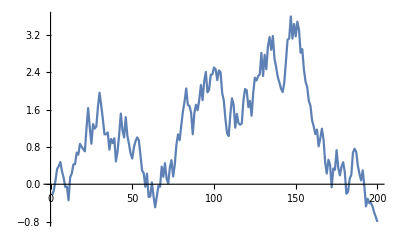

```mathematica
ListLinePlot[DeviceReadList["rw",200]]
```

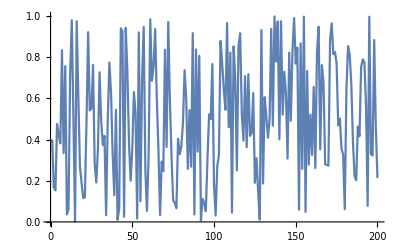

```mathematica
ListLinePlot[DeviceReadList["RandomSignalDemo",200]]
```

DeviceDriverOption also lets you dynamically change the value of the driver function during operation of the device.

Originally, a device of this class reads off the sine of the parameter supplied to DeviceReadpaclet:ref/DeviceRead.

```mathematica
DeviceFramework`DeviceClassRegister["f","ReadFunction"->(Sin[#2]&)];
```

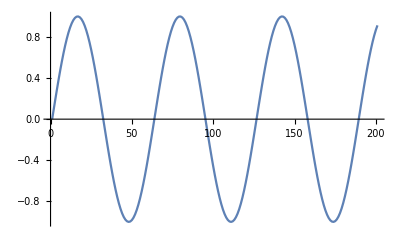

```mathematica
ListLinePlot[Table[DeviceRead["f",i],{i,0,20,.1}]]
```

This changes the driver to read off a sawtooth wave.

```mathematica
DeviceFramework`DeviceDriverOption["f","ReadFunction"]=Mod[#2,5]&;
```

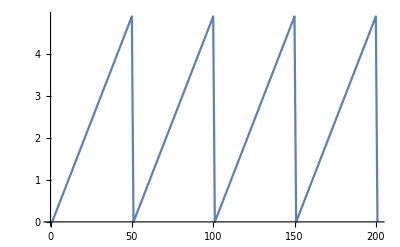

```mathematica
ListLinePlot[Table[DeviceRead["f",i],{i,0,20,.1}]]
```

### The Default Property Handlers

When defining a custom property handler for your class, it is often convenient to call the default handler at some point so that your handler would extend the built-in one rather than recreate it from scratch.

DeviceFramework`DeviceGetProperty[dev,prop] | 
 | execute the default handler for "GetPropertyFunction"
DeviceFramework`DeviceSetProperty[dev,prop,val] | 
 | execute the default handler for "SetPropertyFunction"
DeviceFramework`DeviceDefaultStatusLabels[] | 
 | give a list of the default open and closed status labels
DeviceFramework`DeviceDefaultStatusLabels[p] | 
 | give the default status labels based on the parameter p

Using the default property handlers.

### Class Properties

When the framework needs to assign standardized properties in a particular instance of DeviceObjectpaclet:ref/DeviceObject, it takes the values from class properties. Class properties are specified by the "Properties" options of DeviceClassRegisterpaclet:ref/DeviceClassRegister and can be accessed at any time after the driver is loaded.

DeviceFramework`DeviceClassProperties[class] | 
 | return a list of available properties for the specified class
DeviceFramework`DeviceClassProperties[class,prop] | 
 | return the value of the a property prop for the specified class
DeviceFramework`DeviceClassProperties[class,{p_1,p_2,…}] | 
 | return the values of multiple properties
DeviceFramework`DeviceClassProperties[class,prop]=val,DeviceFramework`DeviceClassProperties[class,{p_1,p_2,…}]={v_1,v_2,…} | 
 | set the values of the the specified properties

Accessing class properties.

Class properties are available even before any device objects are created for the class.

```mathematica
DeviceFramework`DeviceDriverLoad["PropertiesDemo"];
```

```mathematica
DeviceFramework`DeviceClassProperties["PropertiesDemo"]
```

{P1,P2,X}

```mathematica
DeviceFramework`DeviceClassProperties["PropertiesDemo","P1"]
```

p1

Changing device properties does not alter class properties.

```mathematica
dev1=DeviceOpen["PropertiesDemo",1]
```

DeviceObject[…]

```mathematica
dev1["P1"]="newP1";
```

```mathematica
DeviceFramework`DeviceClassProperties["PropertiesDemo","P1"]
```

p1

Conversely, changing class properties does not reset properties of the existing devices, but it does alter properties of new devices in the class.

```mathematica
DeviceFramework`DeviceClassProperties["PropertiesDemo","P1"]="classP1";
```

```mathematica
dev1["P1"]
```

newP1

```mathematica
dev2=DeviceOpen["PropertiesDemo",2]
```

DeviceObject[…]

```mathematica
dev2["P1"]
```

classP1

### Class Preferences

Class preferences, assessed through DeviceClassPreferences, is a more flexible storage for a class, which is persistent between Wolfram Language sessions. Preferences are independent of the device driver, so you can call DeviceClassPreferences before, after, or without ever loading the driver; and that call does not load the driver.

DeviceFramework`DeviceClassPreferences[class] | 
 | return an association of available preferences for the specified class
DeviceFramework`DeviceClassPreferences[class,pref] | 
 | return the value of the preference pref for the specified class
DeviceFramework`DeviceClassPreferences[class,{p_1,p_2,…}] | 
 | return the values of multiple preferences
DeviceFramework`DeviceClassPreferences[class,pref]=val,DeviceFramework`DeviceClassPreferences[class,{p_1,p_2,…}]={v_1,v_2,…} | 
 | set the values of the specified preferences
DeviceFramework`DeviceClassPreferences[class]=assoc | 
 | assign the class preferences to assoc
DeviceFramework`DeviceClassPreferences[class]=.,DeviceFramework`DeviceClassPreferences[class,pref]=.,DeviceFramework`DeviceClassPreferences[class,{p_1,p_2,…}]=. | 
 | clear class preferences or remove the specified keys

Accessing a set of class preferences.

The association of class preferences can contain arbitrary key-value pairs. They are always checked internally at the outset of DeviceClassRegister. If the preferences happen to contain keys corresponding to options of DeviceClassRegister, their values take precedence over options specified in the driver.

Save the "Properties" preferences for a class.

```mathematica
DeviceFramework`DeviceClassPreferences["prefs","Properties"]={"a"->1}
```

{a→1}

When a driver is being created, the value from its preferences is used instead of the value prescribed by the DeviceClassRegister statement, which, in this case, calls for simply copying properties from the parent class.

```mathematica
DeviceFramework`DeviceClassRegister["prefs","PropertiesDemo"];
```

```mathematica
dev=DeviceOpen["prefs"]
```

DeviceObject[…]

```mathematica
dev["Properties"]
```

{a}

```mathematica
DeviceClose[dev]
```

Clear preferences and reevaluate the class definition.

```mathematica
DeviceFramework`DeviceClassPreferences["prefs"]=.
```

```mathematica
DeviceFramework`DeviceClassRegister["prefs","PropertiesDemo"];
```

In the absence of preferences, this class's properties are derived from the parent class, as requested.

```mathematica
dev=DeviceOpen["prefs"]
```

DeviceObject[…]

```mathematica
dev["Properties"]
```

{a,P1,P2,X}

You can set and query device class preferences at any time during a Wolfram Language session. In particular, preferences are useful for storing data needed for device discovery or for simply setting a flag indicating that third-party software required by your driver has been installed on the user's machine.

Devices of this class are not discoverable unless a flag is set in the class preferences.

```mathematica
DeviceFramework`DeviceClassRegister["f","FindFunction"->(If[Lookup[DeviceFramework`DeviceClassPreferences["f"],"installed",False],{{}},{}]&)];
```

```mathematica
FindDevices["f"]
```

{}

After setting the flag, a device can be found.

```mathematica
DeviceFramework`DeviceClassPreferences["f","installed"]=True;
```

```mathematica
FindDevices["f"]
```

{DeviceObject[…]}

### Determining Device State

In addition to top-level functions DeviceOpenpaclet:ref/DeviceOpen, DeviceClosepaclet:ref/DeviceClose, Devicespaclet:ref/Devices, and DeviceOpenQ, which, respectively, open, close, test, and give a list of all devices registered in a current session—whether open or closed—the framework provides several complementing functions for analogous, but less common operations.

DeviceFramework`OpenDevices[] | list of currently open devices
DeviceFramework`DeviceRegisteredQ[dev] | 
 | test whether the device dev is registered in the current Wolfram Langauage session
DeviceFramework`DeviceDeregister[dev] | 
 | deregister and completely remove the device dev from the current session

Testing and changing the device state.

DeviceDeregister also closes a device if it is open. This function can be useful for cleaning slate when developing a driver.

Create a convenience palette to deregister all devices in the current session.

```mathematica
Button["DeregisterAll",DeviceFramework`DeviceDeregister[Devices[]]]//CreatePalette
```

mdngv_shm491FrontEndObject[LinkObject["mdngv_shm", 3, 1]]491Untitled-47

## Inheritance

The Device Framework supports "inheritance". DeviceClassRegister["class","parent",opts] creates a class that is derived from the parent. The explicitly specified options override the ones of the parent. All other options are inherited from the parent. With no options, an alias to the parent is created. Note that the parent can be a string or Nonepaclet:ref/None (the default).

Example: consider the device driver for the demo device "MyPropertiesDemo":

```mathematica
DeviceFramework`DeviceClassRegister["MyPropertiesDemo", "Properties" ->{"P1"->"p1", "P2" -> "p2", "X" -> "x"}];
```

"MyPropertiesDemo" has "Properties" but no "NativeProperties". Next, create a demo device that inherits the properties of "MyPropertiesDemo" and adds its own native properties:

```mathematica
DeviceFramework`DeviceClassRegister["MyPropertiesDemoInherited","MyPropertiesDemo","NativeProperties"->{"N1","N2"}];
```

"MyPropertiesDemo" has "Properties" that can be queried, but lacks "NativeProperties":

```mathematica
mypropDemo = DeviceOpen["MyPropertiesDemo"];
```

```mathematica
mypropDemo["Properties"]
```

{P1,P2,X}

```mathematica
mypropDemo["NativeProperties"]
```

{}

"MyPropertiesDemoInherited" has both "Properties" (inherited from "MyPropertiesDemo") and "NativeProperties":

```mathematica
mypropDemoInh = DeviceOpen["MyPropertiesDemoInherited"];
```

```mathematica
mypropDemoInh["Properties"]
```

{P1,P2,X,NativeProperties}

```mathematica
mypropDemoInh["NativeProperties"]
```

{N1,N2}

## Developing Device Driver Paclets

The Device Framework automatically loads device drivers from the Wolfram paclet servers as if the driver resided locally on your computer. Therefore, whenever you want your drivers to be widely available, you will want to distribute them as paclets.

To create a device driver paclet, include a special file PacletInfo.m in the root device driver directory, parallel to the device driver file. By convention, the name of a driver paclet is the driver class name preceded with "DeviceDriver_"; for instance, "DeviceDriver_MyDevice". Include other supporting files and directories to the root driver directory as needed.

As an example, the device driver for this device, is distributed as a paclet:

```mathematica
DeviceOpen["DocumentationDemo"]
```

DeviceObject[…]

To inspect the contents of the paclet, execute the following command:

```mathematica
DeviceFramework`DeviceDriverFile[%]//DirectoryName//SystemOpen
```

## Examples

### RandomNumberDemo: a Demo Device

"RandomNumberDemo" is a virtual device that outputs a random real number in [0,1] when a read operation is performed. This "device" does not need to be opened, and one can simply start with the "ReadFunction" whose implementation is the Wolfram Language pseudorandom number generation function RandomRealpaclet:ref/RandomReal. Similarly, an n-element buffer read can be simulated via the generation of a random vector.

```mathematica
DeviceFramework`DeviceClassRegister["RandomNumberDemo",
  	"ReadFunction" ->(RandomReal[] &),
  	"ReadBufferFunction" ->(RandomReal[{-1, 1}, #2] &)
     	"DriverVersion"->0.001
  ];
```

```mathematica
DeviceRead["RandomSignalDemo"]
```

0.83505

```mathematica
DeviceReadBuffer["RandomSignalDemo", 15]
```

{0.557971,-0.174465,-0.683969,-0.103215,0.263005,0.556212,0.0521967,-0.952448,0.637859,-0.0207429,-0.0851533,-0.433721,0.852619,-0.953102,0.39118}

### Tinker Forge Weather Station

Tinker Forge Weather Stationhttps://www.tinkerforge.com/en/shop/kits/starter-kit-weather-station.html comprises a set of four ambiance sensors (temperature, pressure, humidity, and illuminance) controlled by a 32-bit ARM micro-controller. The device comes with an attached 20×4 character LCD screen on which strings may be displayed. Each of the three sensors (barometer, humidity, and illuminance) and the LCD screen are treated as a subdevice or "bricklet" sharing a single platform and making up the entire device. A write command from a user would be interpreted as a request to display characters on the LCD screen. The device is connectable to a computer via a mini USB cable.

-Graphics-

Assume that all low-level device communication functions are written in the C programming language using Tinker Forge's C/C++ API bindingshttp://www.tinkerforge.com/en/doc/Downloads.html, and all such .c source files have been compiled into one application (a .exe file) via a build script (e.g. Linux make utility or a .bat file for Windows). Thus, in order to communicate with the device from the Wolfram Language, the first step would be to Installpaclet:ref/Install this executable.

```mathematica
"OpenManagerFunction" -> Install["\path\to\tinkerforge.exe"]
```

This would return a LinkObjectpaclet:ref/LinkObject on which LinkClosepaclet:ref/LinkClose would have to be invoked at the deinitialization stage.

Next, an implementation of the "MakeManagerHandleFunction" returns a handle to an IP connection object representing a TCP/IP connection between the controlling program and the device.

```mathematica
"MakeManagerHandleFunction" -> makeHandleFun
```

where:

```mathematica
makeHandleFun[]:= IPConnectionCreate[]
```

returns an IP Connection object.

```mathematica
ipconn = makeHandleFun[]
```

This connection handle is next used to connect to the individual sensors in "OpenFunction", which returns a list of handles to these sensors. In this case, this list would represent a device object.

```mathematica
"OpenFunction" ->(openFun[#] &)
openFun[ipconn_] := {LightSensorCreate[$lightSensorID, ipconn], 
HumiditySensorCreate[$humSensorID, ipconn], 
BarometerCreate[$pressTempSensorID, ipconn]}
```

"OpenFunction" returns a list of handles {lightSensorHandle,humiditySensorHandle,barometerHandle} that will next be used to query the device for weather data in "ReadFunction". At the user level, the sensor handles would be returned in the form of a device handle upon calling DeviceOpenpaclet:ref/DeviceOpen.

```mathematica
dev = DeviceOpen["TinkerForgeWeatherStation"]
```

Reading sensor data:

```mathematica
"ReadFunction" -> readFun
readFun[{ihandle_, {lightHandle_, humHandle_, baroHandle_}}, rest___] := 
{ReadIlluminanceSensor[lightHandle], ReadHumiditySensor[humHandle], 
ReadBarometer[baroHandle]}
```

This function would return a list of numbers that users would obtain upon calling DeviceReadpaclet:ref/DeviceRead:

```mathematica
weatherData = DeviceRead[dev]
```

Once DeviceReadpaclet:ref/DeviceRead exits, the "CloseFunction" implementation would disconnect the IP connection and explicitly destroy each sensor handle.

```mathematica
"CloseFunction" -> closeFun
closeFun[{ipconn_, {ltHandle_, humHandle_, baroHandle_}}] := 
(IPConnectionDisconnect[ipconn];
  LightSensorDestroy[ltHandle];
  HumiditySensorDestroy[humHandle];
  BarometerDestroy[baroHandle];)
```

A call to closeFun can be initiated by a user through:

```mathematica
DeviceClose[dev]
```

Finally, "ReleaseFunction" is called with the LinkObjectpaclet:ref/LinkObject (returned by Installpaclet:ref/Install) to close the WSTP connection.

```mathematica
"ReleaseFunction" -> releaseFun
releaseFun[link_] := LinkClose[link]
```

## Further Info

Please contact Wolfram Researchhttp://devices.wolfram.com/contact-us.html if you are interested in developing and distributing a device driver for the Wolfram Device Framework.

Related Guides

Using Connected Devices